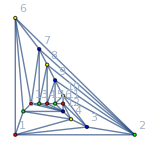
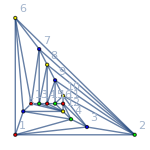
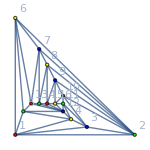
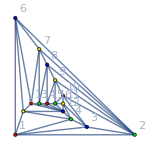
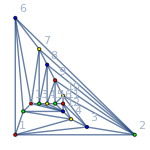
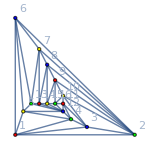
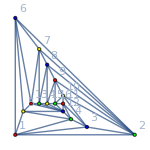
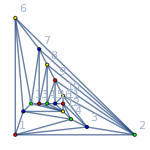

```mathematica
With[{g=Graph[plantri[[6]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->150]},
Map[ColorGraph[g,SymbolToSets[ #]]&,FindFullFormula4[g]]]
```

```mathematica
With[{g=Graph[plantri[[6]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->400]},
Map[SymbolLevel[FilterSymbol[ #,{1,5,13,14,15,16,10,3}]]&,FindFullFormula4[g]]]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
With[{g=VertexDelete[Graph[plantri[[6]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->400],{4,12,11}]},
Map[SymbolLevel[FilterSymbol[ #,{1,5,13,14,15,16,10,3}]]&,FindFullFormula4[g]]]
```

{4,4,4,4,4,4,3,4,4,4,3,3,3,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,4,3,4,4,4,4,4,3,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4}